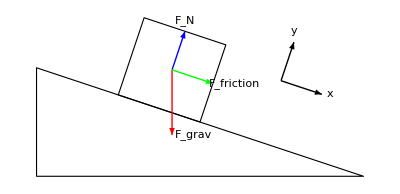

```mathematica
x=Graphics[{
EdgeForm[{Thick}],
FaceForm[],
Triangle[{{0,0},{3,0},{0,1}}],
Polygon[{{3/2,1/2},{3/4,3/4},
{3/40 (10+√10),3/40 (10+3 √10)},
{3/40 (20+√10),1/40 (20+9 √10)}}],
Red,Arrow[{
{1.2435854122563141,0.9807562367689427},
{1.2435854122563141,0.9807562367689427-0.6}
}],
Black,Text["F_grav",{1.2435854122563141+0.2,0.9807562367689427-0.6}],
Blue,Arrow[{
{1.2435854122563141,0.9807562367689427},
{1.3621708245126283,1.3365124735378853}
}],
Black,Text["F_N",{1.3621708245126283,1.3365124735378853+0.1}],
Green,Arrow[{
{1.2435854122563141,0.9807562367689427},
{1.6185854122563141,0.8557562367689426}
}],
Black,Text["F_friction",{1.6185854122563141,0.8557562367689426}+{0.2,0}],
Arrow[{
{1.2435854122563141+1,0.9807562367689427-.1},
{1.3621708245126283+1,1.3365124735378853-.1}
}],
Text["y",{1.3621708245126283+1,1.3365124735378853}],
Arrow[{
{1.2435854122563141+1,0.9807562367689427-.1},
{1.6185854122563141+1,0.8557562367689426-.1}
}],
Text["x",{1.6185854122563141+1.07,0.8557562367689426-.1}]
}]
```

```mathematica
Export["/home/mcard/school/FA23/PHYS019a/figs/upramp.png",x]
```

/home/mcard/school/FA23/PHYS019a/figs/upramp.png

```mathematica
Solve[{
y-3/4==3(x-3/4),
y==-1/3(x-3)+√(5/8)
},{x,y}]
```

{{x→3/40 (10+√10),y→3/40 (10+3 √10)}}

```mathematica
Solve[{
y-2/4==3(x-3/2),
y==-1/3(x-3)+√(5/8)
},{x,y}]
```

{{x→3/40 (20+√10),y→1/40 (20+9 √10)}}

```mathematica
(EuclideanDistance[{3/2,1/2},{3/4,3/4}])^2//N
```

0.625

```mathematica
ArcTan[1/3]//N
```

0.321751

```mathematica
RegionCentroid[Polygon[{{3/2,1/2},{3/4,3/4},
{3/40 (10+√10),3/40 (10+3 √10)},
{3/40 (20+√10),1/40 (20+9 √10)}}]]//N
```

{1.24359,0.980756}

```mathematica
Midpoint[{{3/40 (10+√10),3/40 (10+3 √10)},
{3/40 (20+√10),1/40 (20+9 √10)}}]//N
```

{1.36217,1.33651}

```mathematica
(*Endpoint for f_fric for upramp*)
Midpoint[{{3/2,1/2},{3/40 (20+√10),1/40 (20+9 √10)}}]//N
```

{1.61859,0.855756}

```mathematica
{1.6185854122563141,0.8557562367689426}
```

```mathematica
(*Endpoint for f_fric for downramp*)
Midpoint[{{3/4,3/4},
{3/40 (10+√10),3/40 (10+3 √10)}}]//N
```

{0.868585,1.10576}